```mathematica
SetDirectory[NotebookDirectory[]];
NotebookImport["HEVD.nb",_->"Expression"];
```

```mathematica
(* Unit tests of the [fictiveFlowParams] block] *)
(*
Cases:
 α
u0
Γ
γ
C0
Both ways to calculate Γ
*)
tests=TestReport[
{VerificationTest[((2 Pi Sin[θ]/(2 Cos[θ]+(2 θ - Pi) Sin[θ])-0.9/0.1+1)/.{θ->fictiveFlowParams[0.1,0.9][[1]]})<10^(-10),TestID->"1"],
VerificationTest[
fictiveFlowParams[0.1,0.9][[2]]-(0.9/2* 1/(2 Cos[fictiveFlowParams[0.1,0.9][[1]]]+(2 fictiveFlowParams[0.1,0.9][[1]]+ Pi) Sin[fictiveFlowParams[0.1,0.9][[1]]]))<10^(-10),TestID->"2"],
VerificationTest[fictiveFlowParams[0.1,0.9][[3]]-0.8<10^(-10),TestID->"3"],
VerificationTest[fictiveFlowParams[0.1,0.9][[4]]-Pi-2 fictiveFlowParams[0.1,0.9][[1]]<10^(-10),TestID->"4"],
VerificationTest[fictiveFlowParams[0.1,0.9][[5]]-2fictiveFlowParams[0.1,0.9][[2]] Cos[fictiveFlowParams[0.1,0.9][[1]]]-(Pi+2 fictiveFlowParams[0.1,0.9][[1]]) * Sin[fictiveFlowParams[0.1,0.9][[1]]]<10^(-10),TestID->"5"],
VerificationTest[4*Pi*fictiveFlowParams[0.1,0.9][[2]]*Sin[fictiveFlowParams[0.1,0.9][[1]]],0.8,TestID->"6"]
}
];
```

```mathematica
Print[tests]
```

TestReportObject[…]

{0.100593,0.282072,0.355962,3.34278,0.75067}

{3.48949,3.12382,1.93591}

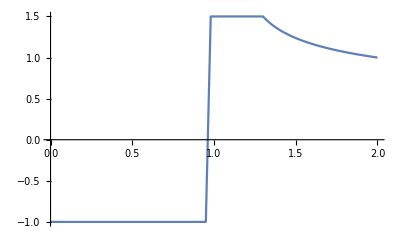

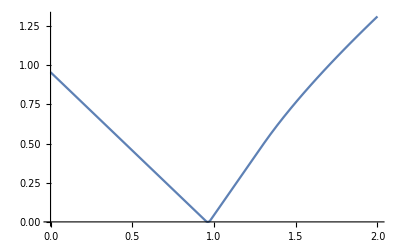

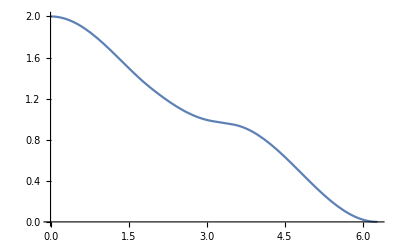

TestReportObject[…]

```mathematica
(* HEVD tests *)
L=2;
v1=1.;
v2=1.5;
s1=0.95;
s2=0.98;
s3=1.3;
k=-1/4;
tr=GCRS[v1,v2,s1,s2,s3,k];
v=tr[[1]];
ϕ=tr[[2]];
s=tr[[3]];
gr1=Plot[v[s],{s,0,L}]
gra=Plot[ϕ[s],{s,0,L}]
gr4=Plot[s[γ],{γ,0,2 Pi}]
testsGCRS=TestReport[
{VerificationTest[v[1.1]-1.5<10^(-10),TestID->"1"],
VerificationTest[ϕ[1.1]-0.1935000000000002<10^(-10),TestID->"2"],
VerificationTest[s[Pi+0.1]-0.9703148716792592<10^(-10),TestID->"3"]
}]
```

```mathematica
testsGCRS
```

TestReportObject[…]

{0.100593,0.282072,0.355962,3.34278,0.75067}

{3.48949,3.12382,1.93591}

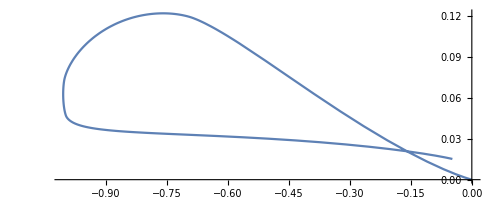

```mathematica
as=Shape[v1,v2,s1,s2,s3,k,1001];x1=as[[1]];y1=as[[2]];ParametricPlot[{x1[γ],y1[γ]},{γ,0,2 Pi}]
```

```mathematica
testsShape=TestReport[
{VerificationTest[x1[Pi]-(-1.001725575740418)<10^(-10),TestID->"1"],
VerificationTest[y1[Pi]-0.07225751231756924<10^(-10),TestID->"2"]
}]
```

TestReportObject[…]

{0.100593,0.282072,0.355962,3.34278,0.75067}

{3.48949,3.12382,1.93591}

Checks 
7.38134×10^-7 
3.23555×10^-7

Lhat = 2.14366

Check s 
2.14366
0.

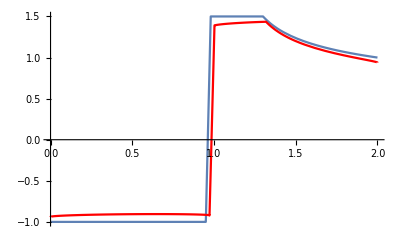

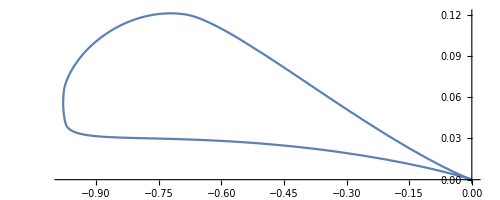

```mathematica
as1=QShape[v1,v2,s1,s2,s3,k,1001];x1=as1[[1]];y1=as1[[2]];ss=as1[[3]];vv=as1[[4]];α=as1[[5]];u0=as1[[6]];grprof1=ParametricPlot[{x1[γ],y1[γ]},{γ,0,2 Pi}];

grnewgcrs=ParametricPlot[{ss[γ],vv[γ]},{γ,0,2 Pi},PlotStyle->{Red}];Show[gr1,grnewgcrs]
Show[grprof1]
```

```mathematica
(* Эти тесты падают из-за точности *)
testsQShape=TestReport[
{VerificationTest[x1[Pi]-(-0.9770718096543248)<10^(-10),TestID->"1"],
VerificationTest[y1[Pi]-(0.06522320791709924)<10^(-10),TestID->"2"],
VerificationTest[ss[Pi]-(1.001476319790847)<10^(-10),TestID->"3"],
VerificationTest[vv[Pi]-(1.277853099943113)<10^(-10),TestID->"4"],
}]
Print["Ручная верификация тестов"]
Print[{x1[Pi],y1[Pi],ss[Pi],vv[Pi]}];
Print[{-0.9770718096543248,0.06522320791709924,1.001476319790847,1.277853099943113}]
testsVel=TestReport[
{VerificationTest[u0-(0.2631687261566028)<10^(-10),TestID->"1"],
VerificationTest[α-(0.1005926874761474)<10^(-10),TestID->"2"]
}]
```

TestReport::invalidexpr: Invalid expression Null.

TestReportObject[…]

Ручная верификация тестов

{-0.977071,0.0652215,1.00148,1.27797}

{-0.977072,0.0652232,1.00148,1.27785}

TestReportObject[…]

{0.261839-0.0264291 ⅈ,0.261838-0.0264282 ⅈ}

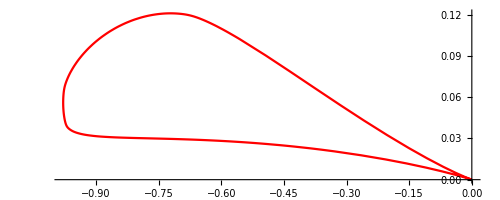

```mathematica
cc=ConfCoeff[x1,y1,50];(*Для отладки,проверка точности:комплексные числа должны быть равны*){cc[[1]],u0 E^(-I α)}
zconf=Evaluate[# horner[cc,1/#]]&;grprof2=ParametricPlot[zz=zconf[E^(I γ)];{Re[zz],Im[zz]},{γ,0,2 Pi},PlotStyle->Red]
```

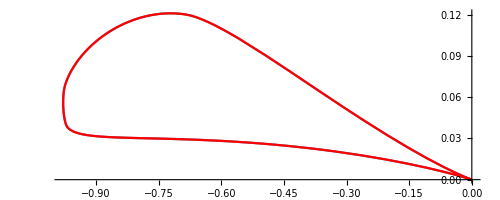

```mathematica
Show[grprof1,grprof2]
```

```mathematica
Print[{x1[Pi],y1[Pi],ss[Pi],vv[Pi]}];
Print[{-0.9770718096543248,0.06522320791709924,1.001476319790847,1.277853099943113}]
```

{-0.977071,0.0652215,1.00148,1.27797}

{-0.977072,0.0652232,1.00148,1.27785}

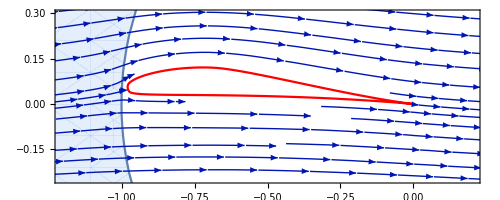

```mathematica
dw[t_]=u0 E^(-I α)(t-E^(I(Pi+2α)))(t-1)/t^2;graf=StreamPlot[zz=dw[x+I y];{Re[zz],-Im[zz]},{x,-3.,3.},{y,-2,2},AspectRatio->Automatic,RegionFunction->Function[{x,y},x^2+y^2>=1]];
gr=Transform[graf,zconf];
Show[gr,grprof2,PlotRange->{{-1.2,0.2},{-0.25,0.3}},ImageSize->500]
```

```mathematica
tr
```

{Piecewise[{{-1., #1<0.95}, {83.3333 (-0.962+#1), 0.95≤#1<0.98}, {1.5, 0.98≤#1<1.3}, {1.5/(1+5.80357 (-1.3+#1))^(1/4), 1.3≤#1}, {0, True}}]&,Piecewise[{{0.006-1. (-0.95+#1), #1<0.95}, {41.6667 (-0.962+#1)^2, 0.95≤#1<0.98}, {0.0135+1.5 (-0.98+#1), 0.98≤#1<1.3}, {0.4935+0.344615 (-1+(1+5.80357 (-1.3+#1))^(3/4)), 1.3≤#1}, {0, True}}]&,Piecewise[{{1.3+0.172308 (-1+(1+2.90179 (0.25717+0.564143 Cos[0.100593-#1]-0.056653 #1))^(4/3)), #1<1.93591}, {0.98+0.666667 (0.73717+0.564143 Cos[0.100593-#1]-0.056653 #1), 1.93591≤#1<3.12382}, {0.962+0.154919 √(0.75067+0.564143 Cos[0.100593-#1]-0.056653 #1), 3.12382≤#1<3.34278}, {0.962-0.154919 √(0.75067+0.564143 Cos[0.100593-#1]-0.056653 #1), 3.34278≤#1<3.48949}, {0.95-1. (0.74467+0.564143 Cos[0.100593-#1]-0.056653 #1), 3.48949≤#1}, {0, True}}]&,0.100593,0.282072}